```mathematica
m[R_]:=-(η+ϵ-ϵ*R)+√((η+ϵ-ϵ*R)^2+4*R*ϵ*η)
```

```mathematica
n[R_]:=(((m[R]^2+4η*m[R]+2*ϵ*m[R]+4η^2+4*ϵ*η+4η)^2-4*(2*m[R]^3+12*η*m[R]^2+24*η^2*m[R]+8*ϵ*η*m[R]+16*η^3+16*ϵ*η^2)))/4(m[R]+2η)
```

```mathematica
ϵ=0.1
```

0.1

```mathematica
R=4.5
```

4.5

```mathematica
η=1
```

1

```mathematica
Clear[R,ϵ,η]
```

```mathematica
Solve[n[R]==0,R]
```

{{R→-10. (-1.045+1. η)-0.5 √(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))-0.5 √(800. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)-0.00333333 (11281.-101200. η+60000. η^2)-(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)-1. (4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)-(0.25 (-64000. (-1.045+1. η)^3+96000. (-1.045+1. η) (0.188017-1.68667 η+1. η^2)-32000. (-0.0261+0.1015 η-1.925 η^2+1. η^3)))/(√(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))))},{R→-10. (-1.045+1. η)-0.5 √(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))+0.5 √(800. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)-0.00333333 (11281.-101200. η+60000. η^2)-(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)-1. (4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)-(0.25 (-64000. (-1.045+1. η)^3+96000. (-1.045+1. η) (0.188017-1.68667 η+1. η^2)-32000. (-0.0261+0.1015 η-1.925 η^2+1. η^3)))/(√(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))))},{R→-10. (-1.045+1. η)+0.5 √(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))-0.5 √(800. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)-0.00333333 (11281.-101200. η+60000. η^2)-(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)-1. (4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(0.25 (-64000. (-1.045+1. η)^3+96000. (-1.045+1. η) (0.188017-1.68667 η+1. η^2)-32000. (-0.0261+0.1015 η-1.925 η^2+1. η^3)))/(√(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))))},{R→-10. (-1.045+1. η)+0.5 √(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))+0.5 √(800. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)-0.00333333 (11281.-101200. η+60000. η^2)-(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)-1. (4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(0.25 (-64000. (-1.045+1. η)^3+96000. (-1.045+1. η) (0.188017-1.68667 η+1. η^2)-32000. (-0.0261+0.1015 η-1.925 η^2+1. η^3)))/(√(400. (-1.045+1. η)^2-600. (0.188017-1.68667 η+1. η^2)+0.00333333 (11281.-101200. η+60000. η^2)+(0.0000111111 (231361.-1.61863×10^9 η+2.34256×10^9 η^2))/(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3)+(4.12165-167929. η+9.49667×10^6 η^2-4.19926×10^6 η^3+1.85185×10^-8 √(0.-2.99688×10^21 η+7.51841×10^25 η^2+7.68332×10^27 η^3+1.93433×10^29 η^4-1.25985×10^29 η^5))^(1/3))))}}

```mathematica
p[η_]:=-10. (-1.045+1. η)+0.5 √(400. (-1.045+1. η)^2-600. (0.18801666666666667-1.6866666666666668 η+1. η^2)+0.0033333333333333335 (11281.-101200. η+60000. η^2)+(0.000011111111111111112 (231361.-1.6186304*^9 η+2.34256*^9 η^2))/(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)+(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3))-0.5 √(800. (-1.045+1. η)^2-600. (0.18801666666666667-1.6866666666666668 η+1. η^2)-0.0033333333333333335 (11281.-101200. η+60000. η^2)-(0.000011111111111111112 (231361.-1.6186304*^9 η+2.34256*^9 η^2))/(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)-1. (4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)+(0.25 (-64000. (-1.045+1. η)^3+96000. (-1.045+1. η) (0.18801666666666667-1.6866666666666668 η+1. η^2)-32000. (-0.0261+0.1015 η-1.925 η^2+1. η^3)))/(√(400. (-1.045+1. η)^2-600. (0.18801666666666667-1.6866666666666668 η+1. η^2)+0.0033333333333333335 (11281.-101200. η+60000. η^2)+(0.000011111111111111112 (231361.-1.6186304*^9 η+2.34256*^9 η^2))/(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)+(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3))))
```

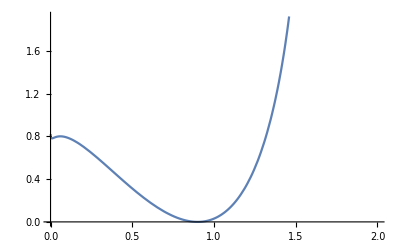

```mathematica
Plot[p[η],{η,0,2}]
```

```mathematica
q[η_]:=-10. (-1.045+1. η)+0.5 √(400. (-1.045+1. η)^2-600. (0.18801666666666667-1.6866666666666668 η+1. η^2)+0.0033333333333333335 (11281.-101200. η+60000. η^2)+(0.000011111111111111112 (231361.-1.6186304*^9 η+2.34256*^9 η^2))/(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)+(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3))+0.5 √(800. (-1.045+1. η)^2-600. (0.18801666666666667-1.6866666666666668 η+1. η^2)-0.0033333333333333335 (11281.-101200. η+60000. η^2)-(0.000011111111111111112 (231361.-1.6186304*^9 η+2.34256*^9 η^2))/(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)-1. (4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)+(0.25 (-64000. (-1.045+1. η)^3+96000. (-1.045+1. η) (0.18801666666666667-1.6866666666666668 η+1. η^2)-32000. (-0.0261+0.1015 η-1.925 η^2+1. η^3)))/(√(400. (-1.045+1. η)^2-600. (0.18801666666666667-1.6866666666666668 η+1. η^2)+0.0033333333333333335 (11281.-101200. η+60000. η^2)+(0.000011111111111111112 (231361.-1.6186304*^9 η+2.34256*^9 η^2))/(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3)+(4.12165337037037-167928.60124444443 η+9.496666177777778*^6 η^2-4.199255703703703*^6 η^3+1.8518518518518518*^-8 √(0.-2.996877932698291*^21 η+7.518412439219357*^25 η^2+7.683318016097945*^27 η^3+1.9343258648956654*^29 η^4-1.2598540894589202*^29 η^5))^(1/3))))
```

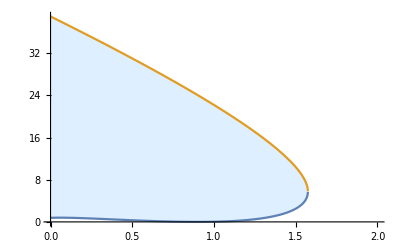

```mathematica
Plot[{p[η],q[η]},{η,0,2},Filling->{1->{{2},{LightBlue,White}}}]
```

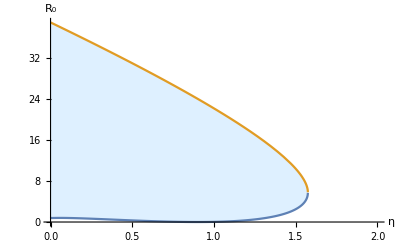

```mathematica
Show[%8,AxesLabel->{HoldForm[η],HoldForm[Subscript[R, 0]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Export["C:\\Users\\Roger Zhang\\Desktop\\0.1.pdf",%9,"PDF"]
```

C:\Users\Roger Zhang\Desktop\0.1.pdf